## KerrEqOfMotGeneral

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"KerrEqOfMotGeneral.wl"
```

This package provides  general solutions of the Kerr geodesic equations in Boyer-Lindquist coordinates. They are given by the following functions
	- ξ[s,{ϵ_r,ξ_0,ε,κ,λ_z,α,δ}] - radial distance;
	- θ[s,{ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - polar coordinate;
	- φ[s,{φ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - azimuthal coordinate;
	- Τ[s,{Τ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - time coordinate;

In order to obtain a complete description of a particular function, write:

```mathematica
?ξ
```

Presenting a particle motion for given initial data is easy

```mathematica
ϕ00=0.33;ϵr=-1;r00=10;ϵth=+1;th00=0.85;ϵ=Sqrt[0.95];λz=3;a=0.8;κ=12;δ=1;
```

Locations of Kerr horizons

```mathematica
rhin=1-√(1-a^2);rhout=1+√(1-a^2);
```

Let us plot the motion in the X-Y plane

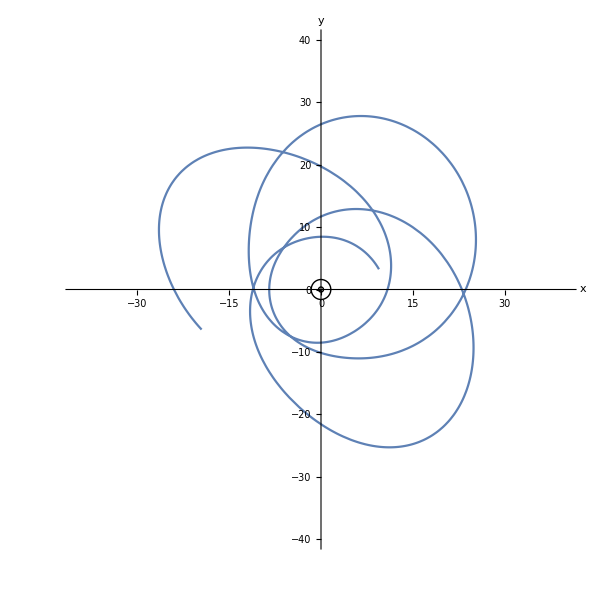

```mathematica
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->{{-40,40},{-40,40}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,AxesLabel->{"x","y"}]
```

Motion in the X-Z plane

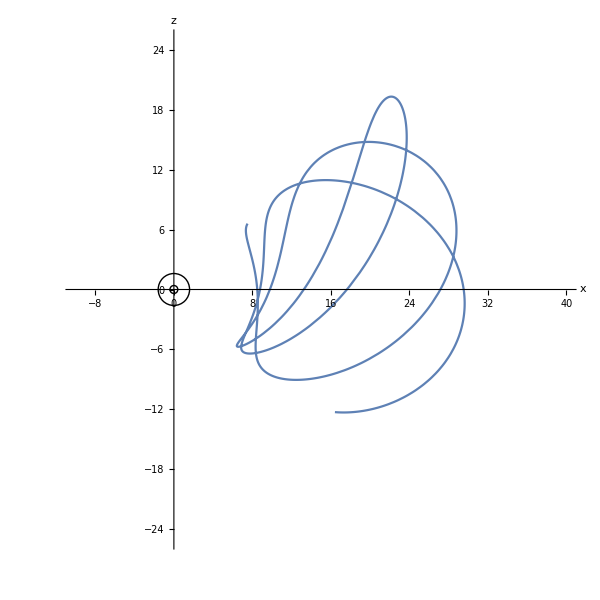

```mathematica
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->{{-10,40},{-25,25}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,
AxesLabel->{"x","z"}]
```

We can make a 3D plot

```mathematica
Show[ParametricPlot3D[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]Cos[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]Sin[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->3{{-10,10},{-10,10},{-10,10}},ImageSize->600,AxesLabel->{"x","y","z"}],SphericalPlot3D[rhout,{θ,0,Pi},{ϕ,0,2Pi}]]
```

-Graphics3D-

The above functions are parametrized by the Mino time s. The package offers a function which convert Mino's time to the proper time τ̃:
					τ̃=M/m tildτ[s,{tildτ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}],
where:
 - tildτ[s,{tildτ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - returns a value of the affine parameter;
	- M - black hole mass;
	- m - particle mas;

We can check how the coordinate time depends on the proper time

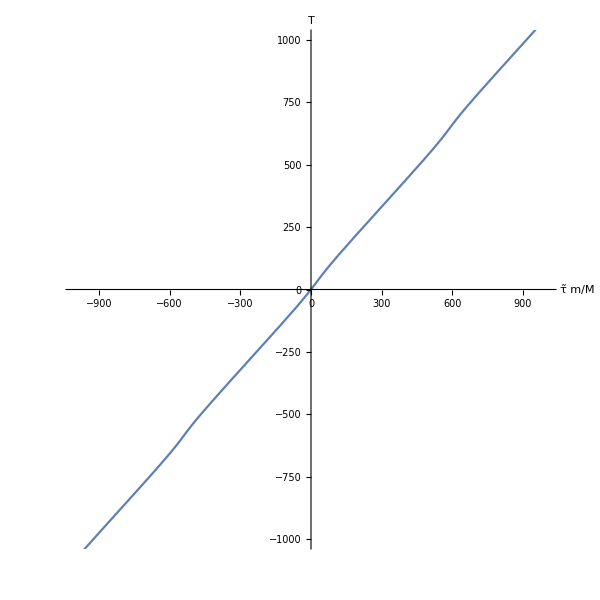

```mathematica
ParametricPlot[{tildτ[s,{ 0,ϵr, r00, ϵth, th00, ϵ, κ, λz, a, δ}],Τ[s,{0, ϵr, r00,  ϵth, th00, ϵ, κ, λz, a, δ}]},{s,-3,3.5},PlotRange->{{-1000,1000},{-1000,1000}},ImageSize->600,AxesLabel->{"τ̃ m/M","Τ"}]
```

The package offers more features, such as

```mathematica
?θmax
```

It contains an implementation of  all functions presented in arXiv:2305.07771, including all elliptic integrals. For example

```mathematica
?I1
```

```mathematica
?I25
```

```mathematica
?K1
```